## Bulk Hamiltonian

### Definitions to be made

```mathematica
Standard Vectors;
yvec={0,1,0};
xvec={1,0,0};
a1vec=1/2{1,1,0};
a1perp=1/2{-1,1,0};
zvec = {0,0,1};

Bravais Vectors;
a1={1,1,0}/2;(*k1=k.a1*)
a2={0,1,1}/2;(*k2=k.a2*)
a3={1,0,1}/2;(*k3=k.a3*)

Reciprocal Vectors;
b1=2Pi{1,1,-1}; 
b2=2Pi{-1,1,1};
b3=2Pi{1,-1,1};

Parameters;
t12=0.9;
t21=0.9;
t11=0.5;
t22=-0.5;
λ=0.7;
mSn=1.65;
mTe=-1.65;

Spin-Orbit;
sx=PauliMatrix[1];
sy=PauliMatrix[2];
sz=PauliMatrix[3];
s0=PauliMatrix[0];

Lx=({{0, 0, 0}, {0, 0, -I}, {0, I, 0}});
Ly=({{0, 0, I}, {0, 0, 0}, {-I, 0, 0}});
Lz=({{0, -I, 0}, {I, 0, 0}, {0, 0, 0}});

Hso=KroneckerProduct[Lx,sx]+KroneckerProduct[Ly,sy]+KroneckerProduct[Lz,sz];
tx=KroneckerProduct[({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}}),s0];(*hop in x-direction along a(1,0,0)*)
ty=KroneckerProduct[({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}),s0];(*hop in y-direction along a(0,1,0)*)
tz=KroneckerProduct[({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}),s0];(*hop in z-direction along a(0,0,1), x1.5*)
tpxpy=KroneckerProduct[({{0.5, 0.5, 0}, {0.5, 0.5, 0}, {0, 0, 0}}),s0]; (*hop in a1-direction along a/2(1,1,0)*)
tpxmy=KroneckerProduct[({{0.5, -0.5, 0}, {-0.5, 0.5, 0}, {0, 0, 0}}),s0]; (*hop in a1'-direction along a/2(1,-1,0)*)
tpxpz=KroneckerProduct[({{0.5, 0, 0.5}, {0, 0, 0}, {0.5, 0, 0.5}}),s0]; (*hop in a3-direction along a/2(1,0,1)*)
tpxmz=KroneckerProduct[({{0.5, 0, -0.5}, {0, 0, 0}, {-0.5, 0, 0.5}}),s0]; (*hop in a3'-direction along a/2(1,0,-1)*)
tpypz=KroneckerProduct[({{0, 0, 0}, {0, 0.5, 0.5}, {0, 0.5, 0.5}}),s0]; (*hop in a2-direction along a/2(0,1,1)*)
tpymz=KroneckerProduct[({{0, 0, 0}, {0, 0.5, -0.5}, {0, -0.5, 0.5}}),s0];(*hop in a2'-direction along a/2(0,1,-1)*)
fz=0.;
onsSn=mSn KroneckerProduct[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1+fz/mSn}}),s0]+λ Hso;
onsTe=mTe KroneckerProduct[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1-fz/mTe}}),s0]+λ Hso;
T={{t11,t12,t11,t12,t12,t11,t12,t11},{0,t22,t21,t22,t22,t21,t22,t21},{0,0,t11,t12,t12,t11,t12,t11},{0,0,0,t22,t22,t21,t22,t21},{0,0,0,0,t22,t21,t22,t21},{0,0,0,0,0,t11,t12,t11},{0,0,0,0,0,0,t22,t21},{0,0,0,0,0,0,0,t11}};
p[x_]:=Exp[I*x]
```

### Matrix Elements

```mathematica
onSiteH={{onsSn,0,0,0,0,0,0,0},
		{0,onsTe,0,0,0,0,0,0},
		{0,0,onsSn,0,0,0,0,0},
		{0,0,0,onsTe,0,0,0,0},
		{0,0,0,0,onsTe,0,0,0},
		{0,0,0,0,0,onsSn,0,0},
		{0,0,0,0,0,0,onsTe,0},
		{0,0,0,0,0,0,0,onsSn}};
```

```mathematica
intraUnitCellH=T*{{0,tx,tpxpz,tz,ty,tpxpy,0,tpypz},
				{0,0,tz,tpxmz,tpxmy,ty,tpypz,0},
				{0,0,0,tx,0,tpymz,ty,tpxmy},
				{0,0,0,0,tpymz,0,tpxpy,ty},
				{0,0,0,0,0,tx,tpxpz,tz},
				{0,0,0,0,0,0,tz,tpxmz},
				{0,0,0,0,0,0,0,tx},
				{0,0,0,0,0,0,0,0}};
```

```mathematica
hopXpos[k_]:=p[k.{1,0,0}]T*{{0,0,0,0,0,0,0,0},
			{0,0,0,tpxpz,tpxpy,0,0,0},
			{0,0,0,tx,0,0,0,tpxpy},
			{0,0,0,0,0,0,0,0},
			{0,0,0,0,0,0,0,0},
			{0,0,0,0,0,0,0,tpxpz},
			{0,0,0,0,0,0,0,tx},
			{0,0,0,0,0,0,0,0}}
```

```mathematica
hopXneg[k_]:=p[k.{-1,0,0}]T*{{0,tx,tpxmz,0,0,tpxmy,0,0},
				{0,0,0,0,0,0,0,0},
				{0,0,0,0,0,0,0,0},
				{0,0,0,0,0,0,tpxmy,0},
				{0,0,0,0,0,tx,tpxmz,0},
				{0,0,0,0,0,0,0,0},
				{0,0,0,0,0,0,0,0},
				{0,0,0,0,0,0,0,0}}
```

```mathematica
hopYneg[k_]:=p[k.{0,-1,0}]T*{{0,0,0,0,ty,tpxmy,0,tpymz},
							{0,0,0,0,tpxpy,ty,tpymz,0},
							{0,0,0,0,0,tpypz,ty,tpxpy},
							{0,0,0,0,tpypz,0,tpxmy,ty},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopZpos[k_]:=p[k.{0,0,1}]T*{{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,tpypz,0,0},
							{0,0,0,0,tpypz,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopZneg[k_]:=p[k.{0,0,-1}]T*{{0,0,tpxmz,tz,0,0,0,tpymz},
							{0,0,tz,tpxpz,0,0,tpymz,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,tpxmz,tz},
							{0,0,0,0,0,0,tz,tpxpz},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopXY[k_]:=p[k.{-1,-1,0}]T*{{0,0,0,0,0,tpxpy,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,tpxpy,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopXYbar[k_]:=p[k.{1,-1,0}]T*{{0,0,0,0,0,0,0,0},
							{0,0,0,0,tpxmy,0,0,0},
							{0,0,0,0,0,0,0,tpxmy},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopXZ[k_]:=p[k.{-1,0,-1}]T*{{0,0,tpxpz,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,tpxpz,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopXZbar[k_]:=p[k.{1,0,-1}]T*{{0,0,0,0,0,0,0,0},
							{0,0,0,tpxmz,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,tpxmz},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopYZ[k_]:=p[k.{0,-1,-1}]T*{{0,0,0,0,0,0,0,tpypz},
							{0,0,0,0,0,0,tpypz,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

```mathematica
hopYZbar[k_]:=p[k.{0,-1,1}]T*{{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,tpymz,0,0},
							{0,0,0,0,tpymz,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0},
							{0,0,0,0,0,0,0,0}}
```

### Final Hamiltonian

```mathematica
hopH[k_]:=intraUnitCellH+hopXpos[k]+hopXneg[k]+hopYneg[k]+hopZpos[k]+hopZneg[k]+hopXY[k]+hopXYbar[k]+hopXZ[k]+hopXZbar[k]+hopYZ[k]+hopYZbar[k]
```

```mathematica
bigH[k_]:=ArrayFlatten[onSiteH/2+hopH[k]]+ConjugateTranspose[ArrayFlatten[onSiteH/2+hopH[k]]]
```

```mathematica
dimH=Length@bigH[{0,0,0}];
```

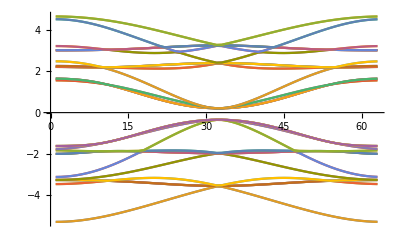

```mathematica
ListLinePlot[Transpose@ParallelTable[Sort@Eigenvalues@bigH[{k,k,1.}],{k,0,2Pi,0.1}]]
```

## Real Space

```mathematica
L1=6;L2=L1;L3=L1;
LBZ=4;
```

```mathematica
a1loc={1,0,0};a2loc={0,1,0};a3loc={0,0,1};
b1loc=2Pi a1loc;b2loc=2Pi a2loc;b3loc=2Pi a3loc;
```

```mathematica
BZ=Flatten[Table[i/LBZ*b1loc+j/LBZ*b2loc+k/LBZ*b3loc,{i,0,LBZ-1},{j,0,LBZ-1},{k,0,LBZ-1}],2];
```

```mathematica
HLoc[k_]:=N@bigH[k];
```

```mathematica
HonS=1/LBZ^3*Sum[HLoc[k],{k,BZ}];
HN1=1/LBZ^3*Sum[Exp[-I k.a1loc]*HLoc[k],{k,BZ}];
HN2=1/LBZ^3*Sum[Exp[-I k.a2loc]*HLoc[k],{k,BZ}];
HN3=1/LBZ^3*Sum[Exp[-I k.a3loc]*HLoc[k],{k,BZ}];
HNN1=1/LBZ^3*Sum[Exp[-I k.(a1loc+a2loc)]*HLoc[k],{k,BZ}];
HNN2=1/LBZ^3*Sum[Exp[-I k.(a2loc+a3loc)]*HLoc[k],{k,BZ}];
HNN3=1/LBZ^3*Sum[Exp[-I k.(a3loc+a1loc)]*HLoc[k],{k,BZ}];
HNN4=1/LBZ^3*Sum[Exp[-I k.(a1loc-a2loc)]*HLoc[k],{k,BZ}];
HNN5=1/LBZ^3*Sum[Exp[-I k.(a2loc-a3loc)]*HLoc[k],{k,BZ}];
HNN6=1/LBZ^3*Sum[Exp[-I k.(a3loc-a1loc)]*HLoc[k],{k,BZ}];
HNS=Chop[{HN1,HN2,HN3,HNN1,HNN2,HNN3,HNN4,HNN5,HNN6}];
```

```mathematica
Lat=Flatten[Table[i*a1loc+j*a2loc+k*a3loc,{i,0,L1-1},{j,0,L2-1},{k,0,L3-1}],2];
```

```mathematica
isNs[i_,j_]:=Block[{diffset=Flatten[Table[Lat[[j]]-(Lat[[i]]+a a1loc L1+b a2loc L2+c a3loc L3),{a,-1,1},{b,-1,1},{c,-1,1}],2]},If[MemberQ[N[diffset],N[a1loc]],1,If[MemberQ[N[diffset],N[a2loc]],2,If[MemberQ[N[diffset],N[a3loc]],3,If[MemberQ[N[diffset],N[a1loc+a2loc]],4,If[MemberQ[N[diffset],N[a2loc+a3loc]],5,If[MemberQ[N[diffset],N[a3loc+a1loc]],6,If[MemberQ[N[diffset],N[a1loc-a2loc]],7,If[MemberQ[N[diffset],N[a2loc-a3loc]],8,If[MemberQ[N[diffset],N[a3loc-a1loc]],9,-1]]]]]]]]]]
```

```mathematica
dist[{i1_,i2_,i3_},{j1_,j2_,j3_}]:=Min[Table[Norm[{i1,i2,i3}-({j1,j2,j3}+a a1loc L1+b a2loc L2+c a3loc L3)],{a,-1,1},{b,-1,1},{c,-1,1}]]
nSet[i_]:=Nearest[Lat->Range[L1 L2 L3],Lat[[i]],19,DistanceFunction->dist][[2;;19]]
sparseList[hpart_,i_,j_,ctrps_]:=If[ctrps,Flatten[Table[{a+(i-1) dimH,b+(j-1) dimH}->Conjugate[hpart[[b,a]]],{a,dimH},{b,dimH}],1],Flatten[Table[{a+(i-1) dimH,b+(j-1) dimH}->hpart[[a,b]],{a,dimH},{b,dimH}],1]]
```

```mathematica
appendlist[i_]:=(prelist={};ns=nSet[i];
For[npos=1,npos≤18,npos++,
j=ns[[npos]];
For[k=1,k≤9,k++,
If[isNs[i,j]==k,AppendTo[prelist,sparseList[HNS[[k]],i,j,False]];AppendTo[prelist,sparseList[HNS[[k]],j,i,True]];Break[]]
]
];Flatten[prelist,1])
ellist=Flatten[ParallelTable[Join[sparseList[HonS,i,i,False],appendlist[i]],{i,L1 L2 L3}],1];H3D=SparseArray[ellist];
```

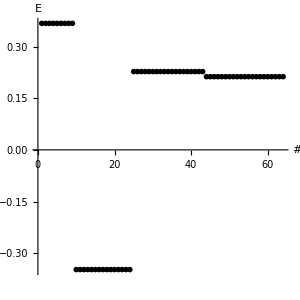

```mathematica
ListPlot[Eigenvalues[H3D,-64],PlotRange->All,AspectRatio->1,ImageSize->300,Ticks->{Automatic,Automatic},AxesStyle->Black,TicksStyle->Directive[Black, 18],PlotStyle->Black,AxesLabel->{"#","E"},LabelStyle->Directive[Black, 18],PlotMarkers->●]
```